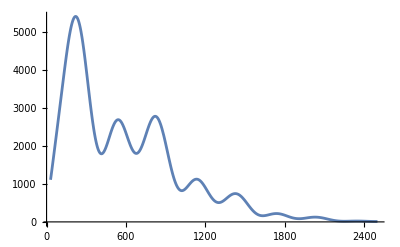

```mathematica
T[k_]:=Log[1+(0.124k)^2]/(0.124k)^2((1+(1.257k)^2+(0.4452k)^4+(0.2197k)^6)/(1+(1.606k)^2+(0.8568k)^4+(0.3927k)^6))^(1/2);
S[k_]:=((1+(1.209k)^2+(0.5116k)^4+5^0.5*(0.1657k)^6)/(1+(0.9459k)^2+(0.4249k)^4+(0.1657k)^6))^2;
Delta[k_]:=(((0.1585k)^2+(0.9702k)^4+(0.2460k)^6)/(1+(1.180k)^2+(1.540k)^4+(0.9230k)^6+(0.4197k)^8))^(1/4);
F[l_]:=519.7*NIntegrate[((b*l)/708)^-0.0418*(1/(b^2*Sqrt[b^2-1])*(3*0.6234*T[b*l/97.6]-(1.6234)^-0.25*S[b*l/97.6]*Exp[-(b*l/1598)^2]*Cos[b*l/96.15+Delta[b*l/97.6]])^2+(3Sqrt[b^2-1])/(b^4*(1.6234)^1.5)*Exp[-2*(b*l/1598)^2]*S[b*l/97.6]^2*Sin[b*l/96.15+Delta[b*l/97.6]]^2),{b,1,Infinity}];
Plot[F[l],{l,30,2500}]
```